# Biconnected Graph

### Author

Eric W. Weisstein
March 22, 2026

This notebook downloaded from https://mathworld.wolfram.com/notebooks/GraphTheory/BiconnectedGraph.nb.

For more information, see Eric's MathWorld entry https://mathworld.wolfram.com/BiconnectedGraph.html.

©2026 Wolfram Research, Inc. except for portions noted otherwise

## Counts

Cf. A002218

### GraphData

```mathematica
Table[Length[GraphData["Biconnected",n]],{n,7}]
```

{0,0,1,3,10,56,468}

### Combinatorica

```mathematica
Table[ConnectedGraphs[i,"Format"->"Combinatorica"],{i,9}];
```

```mathematica
Table[Count[ConnectedGraphs[i,"Format"->"Combinatorica"],_?BiconnectedQ],{i,8}]//Timing
```

{11.8185,{1,1,1,3,10,56,468,7123}}

```mathematica
Table[Count[ConnectedGraphs[i],_?BiconnectedQ],{i,9}]//Timing
```

{345.99,{1,1,1,3,10,56,468,7123,194066}}

### Graphs.m

Load:

```mathematica
Table[ConnectedGraphs[i],{i,10}];//AbsoluteTiming
```

{9552.28,Null}

#### ArticulationVertices (Combinatorica)

```mathematica
Context[ArticulationVertices]
```

Combinatorica`

```mathematica
Table[Count[ConnectedGraphs[i],_?(ArticulationVertices[#]==={}&)],{i,8}]//Timing
```

{0.360945,{1,1,1,3,10,56,468,7123}}

```mathematica
Table[Count[ConnectedGraphs[i],_?(ArticulationVertices[#]==={}&)],{i,9}]//Timing
```

{3.18722,{1,1,1,3,10,56,468,7123,194066}}

```mathematica
Table[Count[ConnectedGraphs[i],_?(ArticulationVertices[#]==={}&)],{i,10}]//Timing
```

{285.222,{1,1,1,3,10,56,468,7123,194066,9743542}}

#### VertexConnectivity

```mathematica
Table[Count[ConnectedGraphs[i],_?(VertexConnectivity[#]>1&)],{i,8}]//Timing
```

{7.29769,{0,0,1,3,10,56,468,7123}}

```mathematica
Table[Count[ConnectedGraphs[i],_?(VertexConnectivity[#]>1&)],{i,9}]//Timing
```

{56.507,{0,0,1,3,10,56,468,7123,194066}}

```mathematica
Table[Count[ConnectedGraphs[i],_?(VertexConnectivity[#]>1&)],{i,10}]//Timing
```

{2768.66,{0,0,1,3,10,56,468,7123,194066,9743542}}

#### KVertexConnectedGraphQ

```mathematica
Table[Count[ConnectedGraphs[i],_?(KVertexConnectedGraphQ[#,2]&)],{i,8}]//Timing
```

{3.51806,{0,0,1,3,10,56,468,7123}}

```mathematica
Table[Count[ConnectedGraphs[i],_?(KVertexConnectedGraphQ[#,2]&)],{i,9}]//Timing
```

{57.6776,{0,0,1,3,10,56,468,7123,194066}}

```mathematica
Table[Count[ConnectedGraphs[i],_?(KVertexConnectedGraphQ[#,2]&)],{i,10}]//Timing
```

{2850.23,{0,0,1,3,10,56,468,7123,194066,9743542}}

#### FindVertexCut

```mathematica
Table[Count[ConnectedGraphs[i],_?(Length[FindVertexCut[#]]>1&)],{i,7}]//Timing
```

{56.7072,{0,0,1,3,10,56,468}}

## Graphic

```mathematica
TextGrid[b={#[[1,1]],Length[#],#[[All,2]]}&/@SplitBy[Sort[GraphData[#,{"V","#"}]&/@GraphData["Biconnected",3;;5]],First],Dividers->All]
```

3 | 1 | {TriangleGraph}
4 | 3 | {DiamondGraph,SquareGraph,TetrahedralGraph}
5 | 10 | {GemGraph,HouseGraph,HouseXGraph,PentatopeGraph,{5,31},{CompleteBipartite,{2,3}},{CompleteTripartite,{1,1,3}},{Cycle,5},{Dipyramid,3},{Wheel,5}}

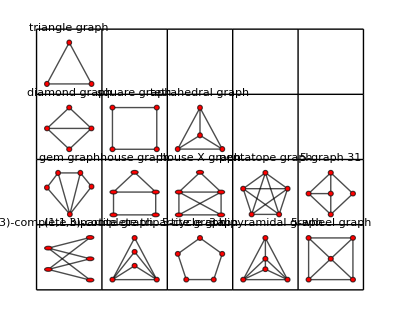

```mathematica
GraphicsGrid[Map[Show[GraphData[#]//StyleGraphs[#,VertexSize->{"Scaled",.08}]&,PlotLabel->TextCell[GraphData[#,"Name"],TextAlignment->Center,PageWidth->75],
LabelStyle->Directive[Black,Italic,FontFamily->"Times"]]&,Flatten[Partition[#,UpTo[5]]&/@b[[All,-1]],1],{2}],ImageSize->400,Dividers->All]
```

#### Connected but Not Biconnected

```mathematica
TextGrid[cnotb={#[[1,1]],Length[#],#[[All,2]]}&/@SplitBy[Sort[GraphData[#,{"V","#"}]&/@Select[GraphData["Connected",;;5],!GraphData[#,"Biconnected"]&]],First],Dividers->All]
```

1 | 1 | {SingletonGraph}
2 | 1 | {{Path,2}}
3 | 1 | {{Path,3}}
4 | 3 | {ClawGraph,PawGraph,{Path,4}}
5 | 11 | {BannerGraph,BullGraph,ButterflyGraph,CricketGraph,DartGraph,ForkGraph,KiteGraph,{Lollipop,{4,1}},{Path,5},{Star,5},{Tadpole,{3,2}}}

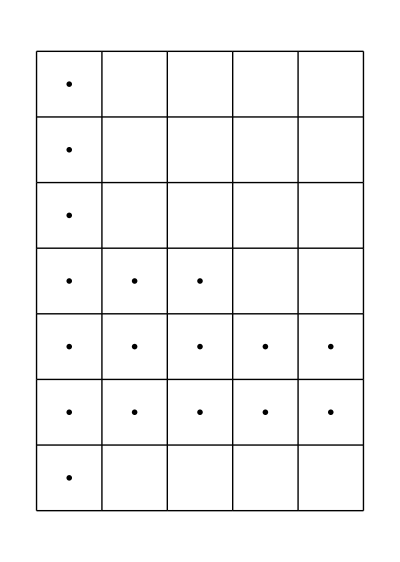

```mathematica
GraphicsGrid[Map[Show[StyleGraphs[GraphData[#],VertexSize->If[#==="SingletonGraph",.03,{"Scaled",.08}]],PlotLabel->TextCell[GraphData[#,"Name"],TextAlignment->Center,PageWidth->75],
LabelStyle->Directive[Black,Italic,FontFamily->"Times"]]&,Flatten[Partition[#,UpTo[5]]&/@cnotb[[All,-1]],1],{2}],ImageSize->400,Dividers->All]
```

## Parametrized families

```mathematica
<<MathWorld`Graphs`
```

### Alkane

```mathematica
seq=Table[GraphData[{"Alkane",n},"Biconnected"],{n,10}]
```

{False,False,False,False,False,False,False,False,False,False}

### AlternatingGroupGraph

```mathematica
seq=Table[GraphData[{"AlternatingGroupGraph",n},"Biconnected"],{n,2,6}]
```

{False,True,True,True,True}

### Andrasfai

```mathematica
seq=Table[GraphData[{"Andrasfai",n},"Biconnected"],{n,20}]
```

{False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Antelope n×n

```mathematica
seq=Table[GraphData[{"Antelope",{n,n}},"Biconnected"],{n,20}]
```

{False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Antiprism

```mathematica
Entity["Graph",{"Antiprism",n}]["Biconnected"]
```

True

```mathematica
MemberQ[CanonicalName@Entity["Graph",{"Antiprism",n}]["Classes"],"Biconnected"]
```

True

```mathematica
seq=Table[GraphData[{"Antiprism",n},"Biconnected"],{n,3,25}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Apollonian

```mathematica
seq=Table[GraphData[{"Apollonian",n},"Biconnected"],{n,6}]
```

{True,True,True,True,True,True}

### Barbell

```mathematica
seq=Table[GraphData[{"Barbell",n},"Biconnected"],{n,3,20}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

### Bishop n×n

```mathematica
seq=Table[GraphData[{"Bishop",{n,n}},"Biconnected"],{n,20}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

### BlackBishop n×n

```mathematica
seq=Table[GraphData[{"BlackBishop",{n,n}},"Biconnected"],{n,20}]
```

{False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Book

```mathematica
seq=Table[GraphData[{"Book",n},"Biconnected"],{n,20}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Bruhat

```mathematica
seq=Table[GraphData[{"Bruhat",n},"Biconnected"],{n,6}]
```

{False,False,True,True,True,True}

### Camel n×n

```mathematica
seq=Table[GraphData[{"Camel",{n,n}},"Biconnected"],{n,20}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

### Cameron

```mathematica
seq=Table[GraphData[{"Cameron",n},"Biconnected"],{n,20}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Centipede

```mathematica
seq=Table[GraphData[{"Centipede",n},"Biconnected"],{n,10}]
```

{False,False,False,False,False,False,False,False,False,False}

### CocktailParty

```mathematica
seq=Table[GraphData[{"CocktailParty",n},"Biconnected"],{n,20}]
```

{False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Complete

```mathematica
Entity["Graph",{"Complete",n}]["Biconnected"]
```

Piecewise[{{False, n==1||n==2}, {True, True}}]

```mathematica
seq=Table[GraphData[{"Complete",n},"Biconnected"],{n,30}]
```

{False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### CompleteBipartite n×n

```mathematica
Entity["Graph",{"CompleteBipartite",{n,n}}]["Biconnected"]
```

Piecewise[{{False, n==1||n==2}, {True, True}}]

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"Biconnected"],{n,20}]
```

{False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### CompleteBipartite m×n

```mathematica
Entity["Graph",{"CompleteBipartite",{m,n}}]["Biconnected"]
```

Piecewise[{{False, Min[m,n]==1}, {True, True}}]

```mathematica
DeleteCases[Flatten[Table[{
{m,n},
GraphData[{"CompleteBipartite",{m,n}},"Biconnected"],
Piecewise[{{False,Min[m,n]==1}},True]
},{n,10},{m,n}],1],{_,x_,x_}]
```

{}

### CompleteTripartite n×n×n

```mathematica
Entity["Graph",{"CompleteTripartite",{n,n,n}}]["Biconnected"]
```

True

```mathematica
MemberQ[CanonicalName@Entity["Graph",{"CompleteTripartite",{n,n,n}}]["Classes"],"Biconnected"]
```

True

```mathematica
seq=Table[GraphData[{"CompleteTripartite",{n,n,n}},"Biconnected"],{n,10}]
```

{True,True,True,True,True,True,True,True,True,True}

### CompleteTripartite k×m×n

```mathematica
Entity["Graph",{"CompleteTripartite",{k,m,n}}]["Biconnected"]
```

True

```mathematica
MemberQ[CanonicalName@Entity["Graph",{"CompleteTripartite",{k,m,n}}]["Classes"],"Biconnected"]
```

True

```mathematica
DeleteCases[Flatten[Table[{
{k,m,n},
GraphData[{"CompleteTripartite",{k,m,n}},"Biconnected"],
True
},{n,10},{m,n},{k,m}],2],{_,x_,x_}]
```

{}

### CompleteTripartiteMinusPerfectMatching

```mathematica
seq=Table[GraphData[{"CompleteTripartiteMinusPerfectMatching",{2n,2n,2n}},"Biconnected"],{n,10}]
```

{True,True,True,True,True,True,True,True,True,True}

### CossidentePenttila

```mathematica
GraphData["CossidentePenttila","Biconnected"]
```

{True,True,True}

### CrossedPrism

```mathematica
seq=Table[GraphData[{"CrossedPrism",2n},"Biconnected"],{n,2,12}]
```

{True,True,True,True,True,True,True,True,True,True,True}

### Crown

```mathematica
seq=Table[GraphData[{"Crown",n},"Biconnected"],{n,20}]
```

{False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### CubeConnectedCycle

```mathematica
Entity["Graph",{"CubeConnectedCycle",n}]["Biconnected"]
```

True

```mathematica
seq=Table[GraphData[{"CubeConnectedCycle",n},"Biconnected"],{n,3,8}]
```

{True,True,True,True,True,True}

### Cycle

```mathematica
Entity["Graph",{"Cycle",n}]["Biconnected"]
```

True

```mathematica
MemberQ[CanonicalName@Entity["Graph",{"Cycle",n}]["Classes"],"Biconnected"]
```

True

```mathematica
seq=Table[GraphData[{"Cycle",n},"Biconnected"],{n,3,30}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### CycleComplement

```mathematica
seq=Table[GraphData[{"CycleComplement",n},"Biconnected"],{n,3,20}]
```

{False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### DiagonalIntersection

```mathematica
seq=Table[GraphData[{"DiagonalIntersection",n},"Biconnected"],{n,3,14}]
```

{True,True,True,True,True,True,True,True,True,True,True,True}

### Dipyramid

```mathematica
seq=Table[GraphData[{"Dipyramid",n},"Biconnected"],{n,3,20}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### DorogovtsevGoltsevMendes

```mathematica
seq=Table[GraphData[{"DorogovtsevGoltsevMendes",n},"Biconnected"],{n,0,7}]
```

{False,True,True,True,True,True,True,True}

### DoubleCone

```mathematica
seq=Table[GraphData[{"DoubleCone",n},"Biconnected"],{n,3,20}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

### Empty

```mathematica
Entity["Graph",{"Empty",n}]["Biconnected"]
```

False

```mathematica
seq=Table[GraphData[{"Empty",n},"Biconnected"],{n,30}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

### FibonacciCube

```mathematica
seq=Table[GraphData[{"FibonacciCube",n},"Biconnected"],{n,15}]
```

{False,False,False,True,True,True,True,True,True,True,True,True,True,True,True}

### Fiveleaper n×n

```mathematica
seq=Table[GraphData[{"Fiveleaper",{n,n}},"Biconnected"],{n,20}]
```

{False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Flower

```mathematica
seq=Table[GraphData[{"Flower",n},"Biconnected"],{n,5,20}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### FoldedCube

```mathematica
seq=Table[GraphData[{"FoldedCube",n},"Biconnected"],{n,2,10}]
```

{False,True,True,True,True,True,True,True,True}

### Gear

```mathematica
seq=Table[GraphData[{"Gear",n},"Biconnected"],{n,3,20}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Giraffe n×n

```mathematica
seq=Table[GraphData[{"Giraffe",{n,n}},"Biconnected"],{n,20}]
```

{False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Goldberg

```mathematica
seq=Table[GraphData[{"Goldberg",n},"Biconnected"],{n,3,20}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Grid n×n

```mathematica
Entity["Graph",{"Grid",{n,n}}]["Biconnected"]
```

Piecewise[{{False, n==1}, {True, True}}]

```mathematica
seq=Table[GraphData[{"Grid",{n,n}},"Biconnected"],{n,20}]
```

{False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Grid m×n

```mathematica
Entity["Graph",{"Grid",{m,n}}]["Biconnected"]
```

Piecewise[{{False, Min[m,n]==1}, {True, True}}]

```mathematica
Sort@DeleteCases[Flatten[Table[{
{m,n},
GraphData[{"Grid",{m,n}},"Biconnected"],
Piecewise[{{False,Min[m,n]==1}},True]
},{n,10},{m,n}],1],{_,x_,x_}]
```

{}

### Grid n×n×n

```mathematica
Entity["Graph",{"Grid",{n,n,n}}]["Biconnected"]
```

Piecewise[{{False, n==1}, {True, True}}]

```mathematica
seq=Table[GraphData[{"Grid",{n,n,n}},"Biconnected"],{n,10}]
```

{False,True,True,True,True,True,True,True,True,True}

### Grid k×m×n

```mathematica
Entity["Graph",{"Grid",{k,m,n}}]["Biconnected"]
```

Piecewise[{{False, Max[k,m,n]==k m n}, {True, True}}]

```mathematica
Sort@DeleteCases[Flatten[Table[{
{k,m,n},
GraphData[{"Grid",{k,m,n}},"Biconnected"],
Piecewise[{{False,Max[k,m,n]==k m n}},True]
},{n,5},{m,n},{k,m}],2],{_,x_,x_}]
```

{}

### HalvedCube

```mathematica
seq=Table[GraphData[{"HalvedCube",n},"Biconnected"],{n,10}]
```

{False,False,True,True,True,True,True,True,True,True}

### Hanoi

```mathematica
seq=Table[GraphData[{"Hanoi",n},"Biconnected"],{n,6}]
```

{True,True,True,True,True,True}

### Helm

```mathematica
seq=Table[GraphData[{"Helm",n},"Biconnected"],{n,3,20}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

### Hypercube

```mathematica
Entity["Graph",{"Hypercube",n}]["Biconnected"]
```

Piecewise[{{False, n==0||n==1}, {True, True}}]

```mathematica
seq=Table[GraphData[{"Hypercube",n},"Biconnected"],{n,0,10}]
```

{False,False,True,True,True,True,True,True,True,True,True}

### KC

```mathematica
DeleteCases[Flatten[Table[{
{m,n},
GraphData[{"KC",{m,n}},"Biconnected"],
True
},{n,3,10},{m,10}],1],{_,x_,x_}]
```

{}

### Keller

```mathematica
Entity["Graph",{"Keller",n}]["Biconnected"]
```

Piecewise[{{False, n==1}, {True, True}}]

```mathematica
seq=Table[GraphData[{"Keller",n},"Biconnected"],{n,5}]
```

{False,True,True,True,True}

### King n×n

```mathematica
seq=Table[GraphData[{"King",{n,n}},"Biconnected"],{n,20}]
```

{False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### King m×n

```mathematica
DeleteCases[Flatten[Table[{
{m,n},
GraphData[{"King",{m,n}},"Biconnected"],
Piecewise[{{False,Min[m,n]==1}},True]
},{n,10},{m,n}],1],{_,x_,x_}]
```

{}

### Knight n×n

```mathematica
Entity["Graph",{"Knight",{n,n}}]["Biconnected"]
```

Piecewise[{{False, n==1||n==2||n==3}, {True, True}}]

```mathematica
seq=Table[GraphData[{"Knight",{n,n}},"Biconnected"],{n,20}]
```

{False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Knight m×n

```mathematica
Entity["Graph",{"Knight",{m,n}}]["Biconnected"]
```

Piecewise[{{False, Min[m,n]<3||m==n==3}, {True, True}}]

```mathematica
DeleteCases[Flatten[Table[{
{m,n},
GraphData[{"Knight",{m,n}},"Biconnected"],
Piecewise[{{False,Min[m,n]<3||m==n==3}},True]
},{n,10},{m,n}],1],{_,x_,x_}]
```

{}

### KP

```mathematica
DeleteCases[Flatten[Table[{
{m,n},
GraphData[{"KP",{m,n}},"Biconnected"],
Piecewise[{{False,m==1||(m==2&&n==1)}},True]
},{n,10},{m,10}],1],{_,x_,x_}]
```

{}

### Ladder

```mathematica
Entity["Graph",{"Ladder",n}]["Biconnected"]
```

Piecewise[{{False, n==1}, {True, True}}]

```mathematica
seq=Table[GraphData[{"Ladder",n},"Biconnected"],{n,20}]
```

{False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### LadderRung

```mathematica
seq=Table[GraphData[{"LadderRung",n},"Biconnected"],{n,20}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

### LindgrenSousselier

```mathematica
seq=Table[GraphData[{"LindgrenSousselier",n},"Biconnected"],{n,11}]
```

{True,True,True,True,True,True,True,True,True,True,True}

### LucasCube

```mathematica
seq=Table[GraphData[{"LucasCube",n},"Biconnected"],{n,15}]
```

{False,False,False,False,True,True,True,True,True,True,True,True,True,True,True}

### MengerSponge

```mathematica
seq=Table[GraphData[{"MengerSponge",n},"Biconnected"],{n,3}]
```

{True,True,True}

### MoebiusLadder

```mathematica
Entity["Graph",{"MoebiusLadder",n}]["Biconnected"]
```

True

```mathematica
MemberQ[CanonicalName@Entity["Graph",{"MoebiusLadder",n}]["Classes"],"Biconnected"]
```

True

```mathematica
seq=Table[GraphData[{"MoebiusLadder",n},"Biconnected"],{n,3,25}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Mycielski

```mathematica
Entity["Graph",{"Mycielski",n}]["Biconnected"]
```

Piecewise[{{False, n==1||n==2}, {True, True}}]

```mathematica
seq=Table[GraphData[{"Mycielski",n},"Biconnected"],{n,11}]
```

{False,False,True,True,True,True,True,True,True,True,True}

### Necklace

```mathematica
seq=Table[GraphData[{"Necklace",n},"Biconnected"],{n,10}]
```

{True,True,True,True,True,True,True,True,True,True}

### Odd

```mathematica
Entity["Graph",{"Odd",n}]["Biconnected"]
```

Piecewise[{{False, n==1}, {True, True}}]

```mathematica
seq=Table[GraphData[{"Odd",n},"Biconnected"],{n,7}]
```

{False,True,True,True,True,True,True}

### Paley

```mathematica
GraphData["Paley","Biconnected"]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Pan

```mathematica
seq=Table[GraphData[{"Pan",n},"Biconnected"],{n,3,20}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

### Path

```mathematica
Entity["Graph",{"Path",n}]["Biconnected"]
```

False

```mathematica
seq=Table[GraphData[{"Path",n},"Biconnected"],{n,20}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

### PathComplement

```mathematica
seq=Table[GraphData[{"PathComplement",n},"Biconnected"],{n,20}]
```

{False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Peisert

```mathematica
GraphData["Peisert","Biconnected"]
```

{True,True,True,True,True,True,True,True}

### Pell

```mathematica
seq=Table[GraphData[{"Pell",n},"Biconnected"],{n,9}]
```

{False,False,True,True,True,True,True,True,True}

### PlummerToft

```mathematica
seq=Table[GraphData[{"PlummerToft",n},"Biconnected"],{n,20}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Prism

```mathematica
Entity["Graph",{"Prism",n}]["Biconnected"]
```

True

```mathematica
MemberQ[CanonicalName@Entity["Graph",{"Prism",n}]["Classes"],"Biconnected"]
```

True

```mathematica
seq=Table[GraphData[{"Prism",n},"Biconnected"],{n,3,25}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Queen n×n

```mathematica
seq=Table[GraphData[{"Queen",{n,n}},"Biconnected"],{n,20}]
```

{False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Rook n×n

```mathematica
seq=Table[GraphData[{"Rook",{n,n}},"Biconnected"],{n,20}]
```

{False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### RookComplement n×n

```mathematica
seq=Table[GraphData[{"RookComplement",{n,n}},"Biconnected"],{n,20}]
```

{False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### SierpinskiCarpet

```mathematica
seq=Table[GraphData[{"SierpinskiCarpet",n},"Biconnected"],{n,4}]
```

{True,True,True,True}

### SierpinskiGasket

```mathematica
seq=Table[GraphData[{"SierpinskiGasket",n},"Biconnected"],{n,7}]
```

{True,True,True,True,True,True,True}

### SierpinskiTetrahedron

```mathematica
seq=Table[GraphData[{"SierpinskiTetrahedron",n},"Biconnected"],{n,6}]
```

{True,True,True,True,True,True}

### Spoke n×n

```mathematica
seq=Table[GraphData[{"Spoke",{n,n}},"Biconnected"],{n,5}]
```

{False,False,False,False,False}

### StackedBook m×n

```mathematica
DeleteCases[Flatten[Table[{
{m,n},
GraphData[{"StackedBook",{m,n}},"Biconnected"],
XXX
},{n,10},{m,n}],1],{_,x_,x_}]
```

{{{1,1},False,XXX},{{1,2},True,XXX},{{2,2},True,XXX},{{1,3},True,XXX},{{2,3},True,XXX},{{3,3},True,XXX},{{1,4},True,XXX},{{2,4},True,XXX},{{3,4},True,XXX},{{4,4},True,XXX},{{1,5},True,XXX},{{2,5},True,XXX},{{3,5},True,XXX},{{4,5},True,XXX},{{5,5},True,XXX},{{1,6},True,XXX},{{2,6},True,XXX},{{3,6},True,XXX},{{4,6},True,XXX},{{5,6},True,XXX},{{6,6},True,XXX},{{1,7},True,XXX},{{2,7},True,XXX},{{3,7},True,XXX},{{4,7},True,XXX},{{5,7},True,XXX},{{6,7},True,XXX},{{7,7},True,XXX},{{1,8},True,XXX},{{2,8},True,XXX},{{3,8},True,XXX},{{4,8},True,XXX},{{5,8},True,XXX},{{6,8},True,XXX},{{7,8},True,XXX},{{8,8},True,XXX},{{1,9},True,XXX},{{2,9},True,XXX},{{3,9},True,XXX},{{4,9},True,XXX},{{5,9},True,XXX},{{6,9},True,XXX},{{7,9},True,XXX},{{8,9},True,XXX},{{9,9},True,XXX},{{1,10},True,XXX},{{2,10},True,XXX},{{3,10},True,XXX},{{4,10},True,XXX},{{5,10},True,XXX},{{6,10},True,XXX},{{7,10},True,XXX},{{8,10},True,XXX},{{9,10},True,XXX},{{10,10},True,XXX}}

### StackedBook n×n

```mathematica
seq=Table[GraphData[{"StackedBook",{n,n}},"Biconnected"],{n,10}]
```

{False,True,True,True,True,True,True,True,True,True}

### StackedPrism m×n

```mathematica
DeleteCases[Flatten[Table[{
{m,n},
GraphData[{"StackedPrism",{m,n}},"Biconnected"],
XXX
},{m,3,8},{n,5}],1],{_,x_,x_}]
```

{{{3,1},True,XXX},{{3,2},True,XXX},{{3,3},True,XXX},{{3,4},True,XXX},{{3,5},True,XXX},{{4,1},True,XXX},{{4,2},True,XXX},{{4,3},True,XXX},{{4,4},True,XXX},{{4,5},True,XXX},{{5,1},True,XXX},{{5,2},True,XXX},{{5,3},True,XXX},{{5,4},True,XXX},{{5,5},True,XXX},{{6,1},True,XXX},{{6,2},True,XXX},{{6,3},True,XXX},{{6,4},True,XXX},{{6,5},True,XXX},{{7,1},True,XXX},{{7,2},True,XXX},{{7,3},True,XXX},{{7,4},True,XXX},{{7,5},True,XXX},{{8,1},True,XXX},{{8,2},True,XXX},{{8,3},True,XXX},{{8,4},True,XXX},{{8,5},True,XXX}}

### StackedPrism n×n

```mathematica
seq=Table[GraphData[{"StackedPrism",{n,n}},"Biconnected"],{n,3,5}]
```

{True,True,True}

### Star

```mathematica
Entity["Graph",{"Star",n}]["Biconnected"]
```

False

```mathematica
seq=Table[GraphData[{"Star",n},"Biconnected"],{n,25}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

### Sun

```mathematica
seq=Table[GraphData[{"Sun",n},"Biconnected"],{n,3,20}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Sunlet

```mathematica
seq=Table[GraphData[{"Sunlet",n},"Biconnected"],{n,3,20}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

### Tetrahedral

```mathematica
seq=Table[GraphData[{"Tetrahedral",n},"Biconnected"],{n,6,10}]
```

{True,True,True,True,True}

### TorusGrid n×n

```mathematica
seq=Table[GraphData[{"TorusGrid",{n,n}},"Biconnected"],{n,3,20}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Transposition

```mathematica
Entity["Graph",{"Transposition",n}]["Biconnected"]
```

Piecewise[{{False, n==1||n==2}, {True, True}}]

```mathematica
seq=Table[GraphData[{"Transposition",n},"Biconnected"],{n,6}]
```

{False,False,True,True,True,True}

### Trapezohedron

```mathematica
Entity["Graph",{"Trapezohedron",n}]["Biconnected"]
```

True

```mathematica
seq=Table[GraphData[{"Trapezohedron",n},"Biconnected"],{n,3,20}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Triangular

```mathematica
seq=Table[GraphData[{"Triangular",n},"Biconnected"],{n,2,20}]
```

{False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### TriangularGrid

```mathematica
seq=Table[GraphData[{"TriangularGrid",n},"Biconnected"],{n,0,20}]
```

{False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### TriangularHoneycombAcuteKnight

```mathematica
seq=Table[GraphData[{"TriangularHoneycombAcuteKnight",n},"Biconnected"],{n,20}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

### TriangularHoneycombBishop

```mathematica
seq=Table[GraphData[{"TriangularHoneycombBishop",n},"Biconnected"],{n,20}]
```

{False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### TriangularHoneycombObtuseKnight

```mathematica
seq=Table[GraphData[{"TriangularHoneycombObtuseKnight",n},"Biconnected"],{n,20}]
```

{False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### TriangularHoneycombQueen

```mathematica
seq=Table[GraphData[{"TriangularHoneycombQueen",n},"Biconnected"],{n,20}]
```

{False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### TriangularHoneycombRook

```mathematica
seq=Table[GraphData[{"TriangularHoneycombRook",n},"Biconnected"],{n,20}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

### TriangularSnake

```mathematica
seq=Table[GraphData[{"TriangularSnake",n},"Biconnected"],{n,1,20,2}]
```

{False,True,False,False,False,False,False,False,False,False}

### TruncatedSquareLattice n×n

```mathematica
seq=Table[GraphData[{"TruncatedSquareLattice",{n,n}},"Biconnected"],{n,10}]
```

{True,True,True,True,True,True,True,True,True,True}

### Web

```mathematica
seq=Table[GraphData[{"Web",n},"Biconnected"],{n,3,20}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

### Wheel

```mathematica
Entity["Graph",{"Wheel",n}]["Biconnected"]
```

False

```mathematica
seq=Table[GraphData[{"Wheel",n},"Biconnected"],{n,4,20}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### WheelComplement

```mathematica
seq=Table[GraphData[{"WheelComplement",n},"Biconnected"],{n,4,20}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

### WhiteBishop n×n

```mathematica
seq=Table[GraphData[{"WhiteBishop",{n,n}},"Biconnected"],{n,2,20}]
```

{False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### WhiteCamel n×n

```mathematica
seq=Table[GraphData[{"Bishop",{n,n}},"Biconnected"],{n,{5}}]
```

{False}

### Zebra n×n

```mathematica
seq=Table[GraphData[{"Zebra",{n,n}},"Biconnected"],{n,20}]
```

{False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}